```mathematica
(* Johannes fitting parameters *)
LCD={{0.0025, 0.01085409,-1.106057,-1.159333},
{0.0900, 0.01085514,-13.493590, 2.150388},
{0.3025, 0.01085640,-39.797327, 24.965545},
{0.6400, 0.01085554,-80.013554, 81.336340},
{1.1025, 0.01085210,-134.141484, 191.491264},
{1.6900, 0.01085481,-202.185387, 379.175010},
{2.4025, 0.01085130,-284.138103, 683.999621},
{3.2400, 0.01086136,-380.015170, 1143.332900},
{4.2025, 0.01085691,-489.792808, 1884.506079},
{5.2900, 0.01085517,-613.485357, 2977.884003},
{6.5025, 0.01084950,-751.085499, 4589.004608},
{7.8400, 0.01084884,-902.604164, 7067.645881},
{9.3025, 0.01084997,-1068.038344, 10667.304476},
{10.8900, 0.01085217,-1247.387431, 16133.941591},
{12.6025, 0.01085409,-1440.650123, 24382.008195},
{14.4400, 0.01084667,-1647.808037, 36688.658380},
{16.4025, 0.01085322,-1868.905655, 52963.123627},
{18.4900, 0.01087420,-2103.948323, 80952.129573},
{20.7025, 0.01085536,-2352.819143, 119013.695269},
{23.0400, 0.01085344,-2615.638250, 190732.889176}};
```

InterpolatingFunction::dmval: Input value {0.000572} lies outside the range of data in the interpolating function. Extrapolation will be used.

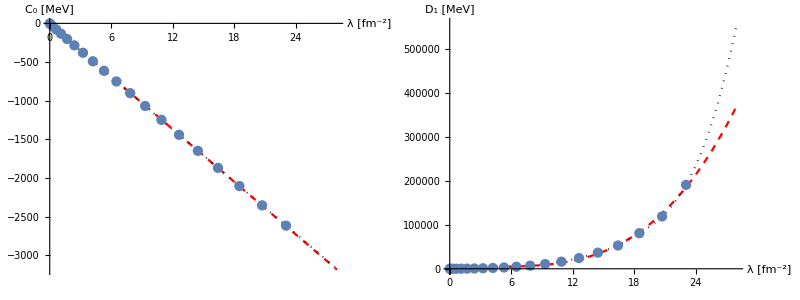

```mathematica
CC=LCD[[;;,3]];DD=LCD[[;;,4]];
λ=LCD[[;;,1]];
Clear[CL,CL2,DL,DL2];
ordc=1;ordd=3;
coeffsc=Array[cpolc,ordc+1];coeffsd=Array[cpold,ordd+1];
modelc=Sum[coeffsc[[n+1]] l^n,{n,0,ordc}];modeld=Sum[coeffsd[[n+1]] l^n,{n,0,ordd}];
lcfit=FindFit[Transpose[{λ,CC}],{modelc},coeffsc,l];ldfit=FindFit[Transpose[{λ,DD}],{modeld},coeffsd,l];
CL[ff_]:=modelc/.lcfit/.l->ff;DL[ff_]:=modeld/.ldfit/.l->ff;
CL2=Interpolation[Transpose[{λ,CC}]];DL2=Interpolation[Transpose[{λ,DD}]];
Grid[{{
Show[Plot[{CL[x],CL2[x]},{x,0,28},PlotStyle->{{Dashed,Red},{Black,Dotted}},AxesLabel->{"λ [fm^-2]","C_0 [MeV]"},ImageSize->Large],ListPlot[Transpose[{λ,CC}],ImageSize->Large]],
Show[Plot[{DL[x],DL2[x]},{x,0,28},PlotStyle->{{Dashed,Red},{Black,Dotted}},AxesLabel->{"λ [fm^-2]","D_1 [MeV]"},ImageSize->Large],ListPlot[Transpose[{λ,DD}],ImageSize->Large]]
}}]
```

```mathematica
Clear[Vex,Vaa];
Vex=Function[{r,rp,α,e,hbc2m},Sqrt[2] α^(3/2) e (-48 Exp[-2 α (r^2+rp^2)]+256/(3 Sqrt[3]) Exp[-10/3 α (r^2+rp^2)] (2 Cosh[16/3 α r rp]))-Sqrt[2] α^(3/2) hbc2m (-48 Exp[-2 α (r^2+rp^2)] (16 r^2 α^2-4 α)+256/(3 Sqrt[3]) Exp[-10/3 α (r^2+rp^2)] (2 Cosh[16/3 α r rp]) (20/3 α)-256/(3 Sqrt[3]) Exp[-10/3 α (r^2+rp^2)] (4/9 α^2 ((100 r^2+64 rp^2) (2 Cosh[16/3 α r rp])-160 r rp (2 Sinh[16/3 α r rp]))))];

Vaa=Function[{r,rp,λ,α,c,d},32/Sqrt[3] c (α/λ)^(3/2) Exp[-(4/3) α r^2]+48 Sqrt[2] d (α/λ)^3 Exp[-2 α r^2]-384 α^3/λ^(3/2) c (Exp[-4 α (r^2+rp^2)] (2 Cosh[4 α r rp])+2 Exp[-2 α (3 r^2+2 rp^2)] (2 Cosh[2 α 4 r rp])-8/3^(3/2) Exp[-(2/3) α (5 r^2+3 rp^2)])-3072 Sqrt[2] α^(9/2)/λ^3 d (Exp[-2 α (3 r^2+3 rp^2)] (2 Cosh[2 α 4 r rp])+4/5^(3/2) Exp[-(2/5) α (19 r^2+11 rp^2)] (2 Cosh[(2/5) α 24 r rp])-4/5^(3/2) Exp[-(2/5) α (11 r^2+11 rp^2)] (2 Cosh[(2/5) α 8 r rp])-1/2^(3/2) Exp[-2 α (2 r^2+rp^2)])];

Vtot=Function[{r,rp,λ,α,c,d,e,hbc2m},Sqrt[2] α^(3/2) e (-48 Exp[-2 α (r^2+rp^2)]+256/(3 Sqrt[3]) Exp[-10/3 α (r^2+rp^2)] (2 Cosh[16/3 α r rp]))-Sqrt[2] α^(3/2) hbc2m (-48 Exp[-2 α (r^2+rp^2)] (16 r^2 α^2-4 α)+256/(3 Sqrt[3]) Exp[-10/3 α (r^2+rp^2)] (2 Cosh[16/3 α r rp]) (20/3 α)-256/(3 Sqrt[3]) Exp[-10/3 α (r^2+rp^2)] (4/9 α^2 ((100 r^2+64 rp^2) (2 Cosh[16/3 α r rp])-160 r rp (2 Sinh[16/3 α r rp]))))+32/Sqrt[3] c (α/λ)^(3/2) Exp[-(4/3) α r^2]+48 Sqrt[2] d (α/λ)^3 Exp[-2 α r^2]-384 α^3/λ^(3/2) c (Exp[-4 α (r^2+rp^2)] (2 Cosh[4 α r rp])+2 Exp[-2 α (3 r^2+2 rp^2)] (2 Cosh[2 α 4 r rp])-8/3^(3/2) Exp[-(2/3) α (5 r^2+3 rp^2)])-3072 Sqrt[2] α^(9/2)/λ^3 d (Exp[-2 α (3 r^2+3 rp^2)] (2 Cosh[2 α 4 r rp])+4/5^(3/2) Exp[-(2/5) α (19 r^2+11 rp^2)] (2 Cosh[(2/5) α 24 r rp])-4/5^(3/2) Exp[-(2/5) α (11 r^2+11 rp^2)] (2 Cosh[(2/5) α 8 r rp])-1/2^(3/2) Exp[-2 α (2 r^2+rp^2)])];
```

```mathematica
hbc2mu=10;
λs={8,16,32,48,128};acore=0.1;
rp=0.5;rma=Max[2 rp,10];ee=0.001;
Animate[
Grid[{{Plot[{Evaluate[Table[Vaa[r,rp,l,aa,CL[l],DL[l]],{l,λs}]],Vex[r,rp,aa,0,hbc2mu]},{r,0.0,rma},PlotLegends->Append[λs,"EX-kernel"],PlotRange->Full,PlotLabels->{Placed[λs,Automatic]},ImageSize->Large],
Plot[Evaluate[Table[Vtot[r,rp,l,aa,CL[l],DL[l],ee,hbc2mu],{l,λs}]],{r,0.0,rma},PlotLegends->λs,AxesLabel->{"r [fm]","EX-Kernel+V_λ"},PlotRange->Full,ImageSize->Large]}}]
,{aa,0.01,0.2},AnimationRunning->True,DefaultDuration->15,AnimationRepetitions->1]
```

```mathematica
rp=0.1;
Animate[
Plot[(Exp[-4 α (r^2+rp^2)] (2 Cosh[4 α r rp])+2 Exp[-2 α (3 r^2+2 rp^2)] (2 Cosh[2 α 4 r rp])-8/3^(3/2) Exp[-(2/3) α (5 r^2+3 rp^2)]),{r,0,2}]
,{α,0.01,0.05},AnimationRunning->False,AnimationRepetitions->1,DefaultDuration->10]
```

```mathematica
rp=0 1.1;
Animate[
Plot[(Exp[-2 α (3 r^2+3 rp^2)] (2 Cosh[2 α 4 r rp])+4/5^(3/2) Exp[-(2/5) α (19 r^2+11 rp^2)] (2 Cosh[(2/5) α 24 r rp])-4/5^(3/2) Exp[-(2/5) α (11 r^2+11 rp^2)] (2 Cosh[(2/5) α 8 r rp])-1/2^(3/2) Exp[-2 α (2 r^2+rp^2)]),{r,0,6}]
,{α,0.01,0.05},AnimationRunning->False,AnimationRepetitions->1,DefaultDuration->10]
```

```mathematica
rp=0 1.1;
Animate[
Plot[Exp[-2 α (r^2+rp^2)]-10/3^(7/2) Exp[-(10/3) α (r^2+rp^2)] (Cosh[(16/3) α r rp]),{r,0,6}]
,{α,0.01,0.05},AnimationRunning->False,AnimationRepetitions->1,DefaultDuration->10]
```